```mathematica
SetDirectory[NotebookDirectory[]];
```

### Compare no corr and corr w=1000

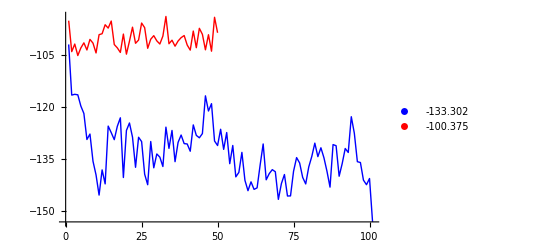

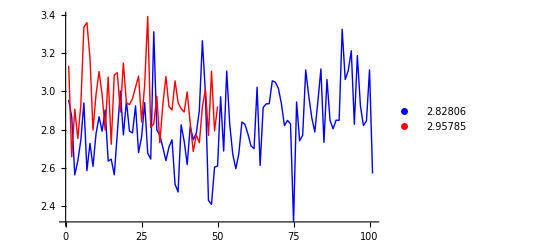

```mathematica
mmin=1;
corrdata=Import["o16ip.vmc1000.dat"];
nocorrdata=Import["o16ip.dmc1000.dat"];
corrE=Transpose[corrdata][[4]];
nocorrE=Transpose[nocorrdata][[4]];
corrσ=Transpose[corrdata][[6]];
nocorrσ=Transpose[nocorrdata][[6]];

ipmean=Mean[corrE[[mmin;;Length[corrdata]]]];
nomean=Mean[nocorrE[[mmin;;Length[nocorrdata]]]];
iperr=Sqrt[Total[corrσ^2]/Length[corrσ]];
noerr=Sqrt[Total[nocorrσ^2]/Length[nocorrσ]];

ListPlot[{nocorrE,corrE},Joined->True,PlotStyle->{{Blue},{Red}},PlotLegends->{nomean,ipmean}]
ListPlot[{nocorrσ,corrσ},Joined->True,PlotStyle->{{Blue},{Red}},PlotLegends->{noerr,iperr}]
```

### Compare no corr and corr w=100 0

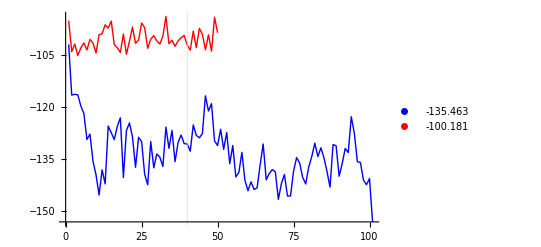

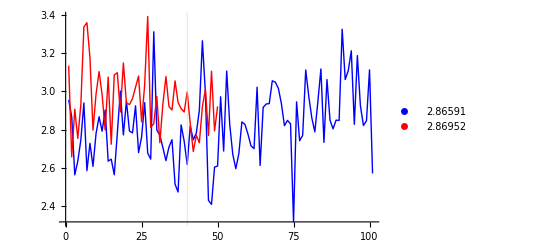

```mathematica
mmin=40;
corrdata=Import["o16ip.vmc1000.dat"];
nocorrdata=Import["o16ip.dmc1000.dat"];
corrE=Transpose[corrdata][[4]];
nocorrE=Transpose[nocorrdata][[4]];
corrσ=Transpose[corrdata][[6]];
nocorrσ=Transpose[nocorrdata][[6]];

corrl=Length[corrE];
nocorrl=Length[nocorrE];
ipmean=Mean[corrE[[mmin;;corrl]]];
nomean=Mean[nocorrE[[mmin;;nocorrl]]];
iperr=Sqrt[Total[corrσ[[mmin;;corrl]]^2]/Length[corrσ[[mmin;;corrl]]]];
noerr=Sqrt[Total[nocorrσ[[mmin;;nocorrl]]^2]/Length[nocorrσ[[mmin;;nocorrl]]]];

ListPlot[{nocorrE,corrE},Joined->True,PlotStyle->{{Blue},{Red}},PlotLegends->{nomean,ipmean},GridLines->{{mmin},{}},GridLinesStyle->Directive[Thick]]
ListPlot[{nocorrσ,corrσ},Joined->True,PlotStyle->{{Blue},{Red}},PlotLegends->{noerr,iperr},GridLines->{{mmin},{}},GridLinesStyle->Directive[Thick]]
```

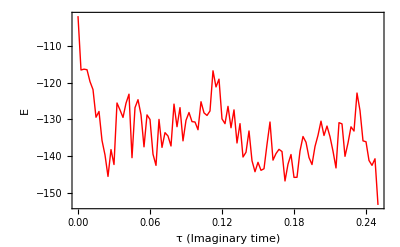

```mathematica
nocorrdata=Import["o16ip.dmc1000.dat"];
pnocorrdata=Transpose[{Transpose[corrdata][[3]],Transpose[corrdata][[4]]}];
corrdata=Import["o16ip.dmc1000.dat"];
pcorrdata=Transpose[{Transpose[corrdata][[3]],Transpose[corrdata][[4]]}];
ListPlot[{pcorrdata},Joined->True,PlotStyle->{Red,Blue},Frame->{{True,False},{True,False}},FrameLabel->{"τ (Imaginary time)","E"},FrameStyle->12,PlotLegends->]
```